# Non-trivial Equilibria Stability Analysis

## Finding Non-Trivial Equilibria & Plotting equilibria with prey birth rate (b) as control

```mathematica
(*Finding the equilibria system*)
ClearAll[phi,psi,A,B,phiPrime,psiPrime,APrime,BPrime,dA,dB,Da,Db,p,m, A1, A2, B1, B2, NumA1, NumA2, NumB1, NumB2, NumEigAtEq1, NumEigAtEq2, EigAtEq1, EigAtEq2];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M={{Da*(1-B)+p*B,Da*A,0,0},{Db*B,Db*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};
(*Vector on the right-hand side*)
RHS = {-s*phi-F[A,B],-s*psi-G[A,B],phi,psi};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
DynSis = Inverse[M].RHS;
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation := DynSis == {0,0,0,0}
```

```mathematica
(*Solving the equilibia equations*)
equilibria = Solve[EquilibriaEquation, {phi, psi, A, B}];
(*Retrieving the 2 non-trivial equilibria points*)
NonTrivialEq = equilibria[[{2,3}]] 
NonTrivialEq1 = equilibria[[2]];
```

{{phi→0,psi→0,A→(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p+(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p)),B→(2 b dA+2 b m+4 b p-2 dB p-√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)},{phi→0,psi→0,A→(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p-(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p)),B→(2 b dA+2 b m+4 b p-2 dB p+√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)}}

```mathematica
EpsParameters = {Db -> ϵ,Da -> ϵ,D -> ϵ, dA -> ϵ^2, dB -> ϵ^2, m -> ϵ^3};
NumericalParameters = {Db -> 0.1, Da ->0.1, D->0.1, dA ->0.01, dB ->0.01,p->0.2, m -> 0.001};
(*NumericalNonTrivialEq = NonTrivialEq/.NumericalParameters*)
```

```mathematica
(* Extracting A and B from the two non-trivial solutions *)
BasicA1 = A /. NonTrivialEq[[1]]
BasicB1 = B /. NonTrivialEq[[1]]
A1[b_] := (A /. NonTrivialEq[[1]]);
B1[b_] := (B /. NonTrivialEq[[1]]);
A2[b_] := (A /. NonTrivialEq[[2]]);
B2[b_] := (B /. NonTrivialEq[[2]]);
(*Finding the equivalent non-trivial solutions with numerical parameters*)
NumA1[b_] := (A /. NonTrivialEq[[1]]) /. NumericalParameters;
EpsA1[b_] := (A /. NonTrivialEq[[1]]) /. EpsParameters;
FullSimplify[NumA1[b]];
Series[EpsA1[b],{ϵ,0,4}];
NumB1[b_] := (B /. NonTrivialEq[[1]]) /. NumericalParameters;
EpsB1[b_] := (B /. NonTrivialEq[[1]]) /. EpsParameters;
Series[EpsB1[b],{ϵ,0,4}];
(*These are not physically relevant, B2 is negative for whatever b parameter*)
NumA2[b_] := (A /. NonTrivialEq[[2]]) /. NumericalParameters;
EpsA2[b_] := (A /. NonTrivialEq[[2]]) /. EpsParameters;
Series[EpsA2[b],{ϵ,0,3}];
NumB2[b_] := (B /. NonTrivialEq[[2]]) /. NumericalParameters;
EpsB2[b_] := (B /. NonTrivialEq[[2]]) /. EpsParameters;
Series[EpsB2[b],{ϵ,0,3}];
```

(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p+(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p))

(2 b dA+2 b m+4 b p-2 dB p-√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)

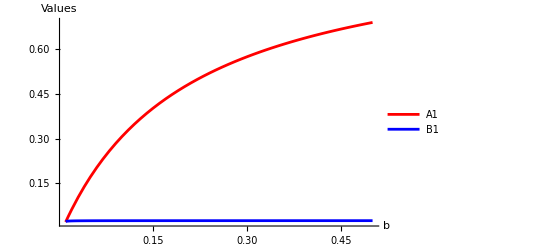

```mathematica
Plot[{NumA1[b], NumB1[b]}, {b, 0.01, 0.5},
     PlotLegends -> {"A1", "B1"},
     PlotStyle -> {Red, Blue},
     AxesLabel -> {"b", "Values"},
     PlotRange -> All]
```

```mathematica
Export["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/NonTrivialEquilibriaPlot.pdf",
	Plot[{NumA1[b], NumB1[b], NumA2[b], NumB2[b]}, {b, 0.01, 0.5},
	 PlotLegends -> {Style[Superscript[Subscript["A", "2"], "*"], Italic], Style[Superscript[Subscript["B", "2"], "*"], Italic], Style[Superscript[Subscript["A", "3"], "*"], Italic], Style[Superscript[Subscript["B", "3"], "*"],Italic]},
	 PlotStyle -> {
	   Directive[Red, Thickness[0.004]],
	   Directive[Blue, Thickness[0.004]],
	   Directive[Green, Thickness[0.004]],
	   Directive[Orange, Thickness[0.004]]
	   },
	 AxesLabel -> {Style["b",Italic], "Value"},
	 LabelStyle -> {FontSize -> 10},
	 GridLines -> Automatic,
	 PlotRange -> All(*,
	 PlotLabel -> 
	 Row[{
	   "Non-trivial equilibria ", 
	   Style[Superscript[Subscript["X", "2"], "*"], Italic], " and ",
	   Style[Superscript[Subscript["X", "3"], "*"], Italic]
	 }]*)
	 ]
]
SystemOpen["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/NonTrivialEquilibriaPlot.pdf"]
```

/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/NonTrivialEquilibriaPlot.pdf

To better understand which equilibria are physically relevant, one most

```mathematica
Export["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/CloseToZeroEquilibria.pdf",
	Plot[{NumB1[b],NumA2[b]}, {b, 0.01, 0.5},
     PlotLegends -> {Style[Superscript[Subscript["B", "2"], "*"], Italic],Style[Superscript[Subscript["A", "3"], "*"], Italic]},
     PlotStyle -> {
          Directive[Blue,Thickness[0.004]],
          Directive[Green, Thickness[0.004]]  
     },
     AxesLabel -> {Style["b",Italic], "Value"},
     LabelStyle->{FontSize -> 10},
     GridLines->Automatic,
     PlotRange -> All]
]
SystemOpen["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/CloseToZeroEquilibria.pdf"]
```

/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/CloseToZeroEquilibria.pdf

Here we note that the second equilibria, corresponding to  is not physically relevant as the quantity A2 is negative.

We now plot the rescaled system, considering the scaling B = ϵ ^2 B0

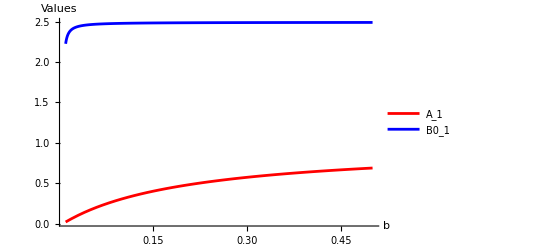

```mathematica
Clear[ϵ]
ϵ = 0.1;
Plot[{NumA1[b], NumB1[b]/ϵ^2}, {b, 0.01, 0.5},
     PlotLegends -> {"A_1", "B0_1"},
     PlotStyle -> {Red, Blue},
     AxesLabel -> {"b", "Values"},
     PlotRange -> All]
Clear[ϵ]
```

# Stability Analysis - Computation of the Jacobian & Eigenvalues

```mathematica
(*Jacobian computation & Evalutation At Equilibria*)
JacobianMatrix := D[DynSis,{{phi, psi, A, B}}];
(*JacAtEq1 = JacobianMatrix /. {phi -> 0, psi ->0, A -> A1[b], B -> B1[b]}*)
JacAtEq1 := JacobianMatrix /. {phi -> 0, psi ->0 , A -> BasicA1, B -> BasicB1};
JacAtEq2 = JacobianMatrix /. {phi -> 0, psi ->0,A -> A2[b], B -> B2[b]};
NumJacAtEq1 := JacAtEq1 /. NumericalParameters;
NumJacAtEq2 = JacAtEq2 /. NumericalParameters;
```

## Eigenvalues for Non-Trivial Equilibrium 1 (Predator prevails A1 =1, B1 = 0)

```mathematica
(*(*LATEST IDEA, FIST EIGENVALUE CALCULATION THEN NUMERICAL REPLACEMENT
This idea does not work as the expression to compute the eigenvalues of JacAtEq1 is rather complex*)
ClearAll[EigJacAtEq1, Eig1AtEq1,Eig2AtEq1,Eig3AtEq1,Eig4AtEq1,NumEig1AtEq1,NumEig2AtEq1];
EigJacAtEq1 = Eigenvalues[JacAtEq1];
Eig1AtEq1 = EigJacAtEq1[[1]]
Eig2AtEq1 = EigJacAtEq1[[2]];
Eig3AtEq1 = EigJacAtEq1[[3]];
Eig4AtEq1 = EigJacAtEq1[[4]];
NumEig1AtEq1[b_,s_] = Eig1AtEq1 /. NumericalParameters;
NumEig2AtEq1[b_,s_] = Eig2AtEq1 /. NumericalParameters;
NumEig3AtEq1[b_,s_] = Eig3AtEq1 /. NumericalParameters;
NumEig4AtEq1[b_,s_] = Eig4AtEq1 /. NumericalParameters;*)
```

$Aborted

Part::partd: Part specification EigJacAtEq1⟦1⟧ is longer than depth of object.

EigJacAtEq1⟦1⟧

Part::partd: Part specification EigJacAtEq1⟦2⟧ is longer than depth of object.

Part::partd: Part specification EigJacAtEq1⟦3⟧ is longer than depth of object.

Part::partd: Part specification EigJacAtEq1⟦4⟧ is longer than depth of object.

```mathematica
(*INITIAL IDEA, FIST NUMERICAL REPLACEMENT, THEN EIGENVALUE CALCULATION)*)
(*Makes a huge difference to hold all and first evaluate then afterwards just evaluate*)
(*Computing the numerical eigenvalues of the resulting numerical jacobian*)
ClearAll[NumEigAtEq1,NumEig1AtEq1,NumEig2AtEq1,NumEig3AtEq1,NumEig4AtEq1]
NumEigAtEq1 := Eigenvalues[NumJacAtEq1];
NumEig1AtEq1[b_,s_] := NumEigAtEq1[[1]];
NumEig2AtEq1[b_,s_] := NumEigAtEq1[[2]];
NumEig3AtEq1[b_,s_] := NumEigAtEq1[[3]];
NumEig4AtEq1[b_,s_] := NumEigAtEq1[[4]];
```

```mathematica
Export["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/stabilityNonTrivialEquilibrium.pdf",
	GraphicsGrid[{{
	Plot3D[
	 Re[NumEig1AtEq1[b,s]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen1)", 
	 AxesLabel -> {"b", "s", "Re(eigen10"}, 
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0.0, Green, 
	      z < 0.0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}
	],
	Plot3D[
	 Re[NumEig2AtEq1[b, s]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen2)",
	 AxesLabel -> {"b", "s", "Re(eigen2)"},
	
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0.0, Green, 
	      z < 0.0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	 
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}
	]},{
	Plot3D[
	 Re[NumEig3AtEq1[b, s]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen3)", 
	 AxesLabel -> {"b", "s", "Re(eigen3)"},
	
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0, Green, 
	      z < 0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}
	],
	Plot3D[
	 Re[NumEig4AtEq1[b, s]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen4)", 
	 AxesLabel -> {"b", "s", "Re(eigen4)"}, 
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0, Green, 
	      z < 0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}]}}
	 ]
 ]
 SystemOpen["/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/stabilityNonTrivialEquilibrium.pdf"]
```

/Users/henriquecolacoecaldas/Library/Mobile Documents/com~apple~CloudDocs/01_Munich/01_TUM/01_Master/05_Fifth_Semester/Master Thesis/02_Figures/equilibria/stabilityNonTrivialEquilibrium.pdf

```mathematica
(*Plot the fucntion for which there is sign change in the eigenvalues for fixed s*)
Plot[Re[NumEig1AtEq1[b,s]]/.{s->0.1},{b,0.01,0.2}, PlotRange->{-50,50}]
Plot[Re[NumEig2AtEq1[b,s]]/.{s->0.1},{b,0.01,0.2}, PlotRange->{-50,50}]
```

-Graphics-

-Graphics-

```mathematica
Plot3D[
	 Re[NumEigAtEq1[b, s][[1]]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen1)", 
	 AxesLabel -> {"b", "s", "Re(eigen10"}, 
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0.0, Green, 
	      z < 0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}
	]
Plot3D[
	 Re[NumEigAtEq1[b, s][[2]]],
	 {b,  0.01, 0.2}, {s, 0, 0.2},
	 PlotLabel -> "Re(eigen2)",
	 AxesLabel -> {"b", "s", "Re(eigen2)"},
	
	 ColorFunction -> Function[{x, y, z}, 
	    Which[
	      z > 0.0, Green, 
	      z < 0.0, Red, 
	      True, Yellow
	    ]
	  ], 
	 ColorFunctionScaling -> False,
	 MeshFunctions -> {#3 &},
	 MeshStyle -> {{Thin, Black}},
	 
	 (* Ensure full z-range is displayed *)
	 PlotRange -> All, 
	 Ticks -> {Automatic, Automatic, Automatic}
	]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Test for specific values*)
Re[N[NumEigAtEq1[b,s][[1]]]] /. {b->0.02, s->0.}
```

0.02

## Eigenvalues for Non - Trivial Equilibrium 2 (Prey prevails, A2= 0, B2 =1)

```mathematica
(*Computing the numerical eigenvalues of the resulting numerical jacobian*)
NumEigAtEq2[b_,s_] := Eigenvalues[NumJacAtEq2];

Plot3D[
 Re[NumEigAtEq2[b, s][[1]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of Eigenvalue 1 vs b and s", 
 AxesLabel -> {"b", "s", "Re"}, 

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Re[NumEigAtEq2[b, s][[2]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of Eigenvalue 2 vs b and s",
 AxesLabel -> {"b", "s", "Re"},

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Im[NumEigAtEq2[b, s][[3]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of Eigenvalue 3 vs b and s", 
 AxesLabel -> {"b", "s", "Re"},

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
Plot3D[
 Im[NumEigAtEq2[b, s][[4]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of Eigenvalue 4 vs b and s", 
 AxesLabel -> {"b", "s", "Re"}, 

 ColorFunction -> Function[{x, y, z}, 
    Which[
      z > 0, Green, 
      z < 0, Red, 
      True, Yellow
    ]
  ], 
 ColorFunctionScaling -> False,
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}},
 
 (* Ensure full z-range is displayed *)
 PlotRange -> All, 
 Ticks -> {Automatic, Automatic, Automatic}
]
```

-Graphics3D-

Part::partw: Part 2 of Eigenvalues[NumJacAtEq2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

Part::partw: Part 3 of Eigenvalues[NumJacAtEq2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

Part::partw: Part 4 of Eigenvalues[NumJacAtEq2] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-